```mathematica
x={1.02,0.95,0.87,0.77,0.67,0.56,0.44,0.30,0.16,0.01};
y={0.39,0.32,0.27,0.22,0.18,0.15,0.13,0.12,0.13,0.15};
list=Transpose[{x,y}];
A =Table[1,{i,10},{j,5}]; (*Initialize matrix*)
f={y^2,x y,x,y, 1-x+x};
For[i=1,i<11,i++,For[j=1,j<6,j++,A[[i,j]]=f[[j,i]]]]; (*Fill matrix*)
```

```mathematica
r=x^2;
```

```mathematica
LeastSquares[A,r]; (*Use least squares routine*)
```

```mathematica
coeff={-2.635625483712139,0.1436461825989035,0.5514469631403562,3.2229403381059027,-0.4328942702644508};
```

```mathematica
func={g^2,d g,d,g,1}.coeff;
```

```mathematica
x2=x+RandomReal[{-0.005,0.005},Length[x]];
y2=y+RandomReal[{-0.005,0.005},Length[y]]; (*Adjust data*)
```

```mathematica
list2=Transpose[{x2,y2}];
```

```mathematica
f={y2^2,x2 y2,x2,y2, 1-x2+x2}
```

{{0.149738,0.101267,0.0722012,0.0503564,0.030951,0.0226869,0.01676,0.0140377,0.0157404,0.0217487},{0.39383,0.303889,0.2336,0.17232,0.118505,0.0846354,0.0572928,0.0351872,0.0202485,0.00195965},{1.01775,0.95495,0.869363,0.767905,0.673597,0.561907,0.442551,0.296987,0.161393,0.0132881},{0.38696,0.318225,0.268703,0.224402,0.175929,0.150622,0.12946,0.118481,0.125461,0.147474},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
For[i=1,i<11,i++,For[j=1,j<6,j++,A[[i,j]]=f[[j,i]]]];
```

```mathematica
q2=x2^2;
```

```mathematica
coef2=LeastSquares[A,q2]
```

{-3.60225,0.816468,0.447883,3.06636,-0.385531}

```mathematica
func2={g^2,d g,d,g,1}.coef2;
```

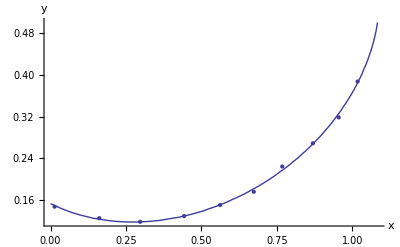

```mathematica
Show[ListPlot[list2],ContourPlot[func2==d^2,{d,0,2},{g,0,0.5}],AxesLabel->{"x","y"}]
```

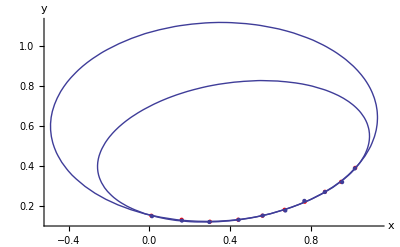

```mathematica
Show[ListPlot[list,PlotStyle->{Red,PointSize[Large]}],ListPlot[list2],ContourPlot[func2==d^2,{d,-0.9,2.0},{g,0,1.8}],ContourPlot[func==d^2,{d,-0.9,2.0},{g,0,1.8}],AxesLabel->{"x","y"}]
```

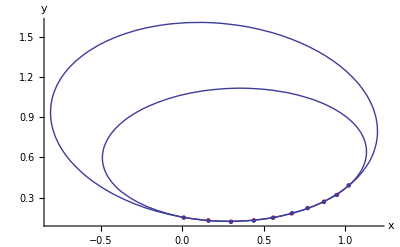

-Graphics-